# Fractal Dimension calculator

## Import the image

To import the image, just copy and paste it down below;

```mathematica
img = -Graphics-
bin = LocalAdaptiveBinarize[ImageAdjust[img,0.3],128,{0.9,0,0}]
bin = ImageResize[bin,{2*3*5*7*11,2*3*5*7*11}]
```

-Graphics-

-Graphics-

-Graphics-

## Compute the possible box sizes

choose box sizes in pixels so that an integer number of boxes fit in the image

```mathematica
seq = Reverse[Intersection @@ Divisors /@ ImageDimensions[bin]]
```

{2310,1155,770,462,385,330,231,210,165,154,110,105,77,70,66,55,42,35,33,30,22,21,15,14,11,10,7,6,5,3,2,1}

## BoxCount

This is it, where you count boxes

```mathematica
{width, height} = ImageDimensions[bin]

result = {
  width/#, 
  Last@First@ImageLevels@Image[
      BlockMap[Min, ImageData[bin], {#, #}],
      "Bit"]
  } & /@ seq;
```

{2310,2310}

## Plot Result

Here you can see how well the linear Relation fits the data

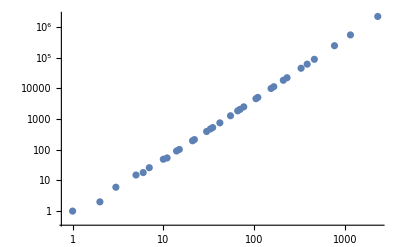

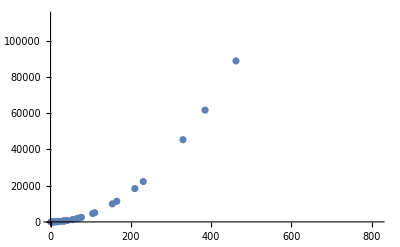

```mathematica
ListLogLogPlot[result]
ListPlot[result]
```

```mathematica
fm = LinearModelFit[Log[result], {1, x}, x]
```

FittedModel[0.576479+1.42517 x]

Of course, the slope of the line is the dimension of the fractal

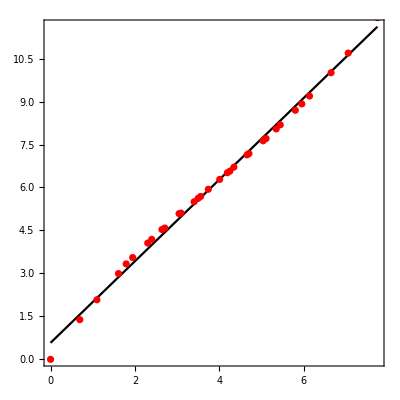

```mathematica
plot = Show[
  Plot[fm[x], {x, Log[result[[1, 1]]], Log[result[[-1, 1]]]}, 
   PlotStyle -> Black],
  ListLogLogPlot[result, PlotStyle -> Red],
  AspectRatio -> 1, Axes -> False, Frame -> True
  ]
```

```mathematica
sz = 252;
imgs = Image[BlockMap[Min, ImageData[bin], {#, #}], "Bit"] & /@ seq
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Animation

```mathematica
imgs = If[First@ImageDimensions[#] > sz, 
     ImageResize[Image[#, Real], sz], 
     ImageResize[#, sz, Resampling -> "Nearest"]] & /@ imgs; 

frm = Table[
  ImageCompose[ImageResize[bin, 252], {im, 0.5}], {im, imgs}];
```

```mathematica
frames = Table[
   Row[{
     Show[plot, ImageSize -> 400, 
      Epilog -> {AbsolutePointSize[10], Red, Point@Log[result[[i]]]}],
      Image[frm[[i]], Magnification -> 1]
     }],
   {i, Length[imgs]}];

ListAnimate[frames]
```

### Many thanks to Slabolcs Horvàt

check his work here, http://community.wolfram.com/groups/-/m/t/1025046